```mathematica
{Slider[Dynamic[t],{1,20,5}],Dynamic[t]}
Dynamic[Plot[{Evaluate[Table[x,{x,2n}]],n/Sqrt[2]+n*Cos[x],n/Sqrt[2]+n*Sin[x]},{x,0,2π}]]
```

{,}

```mathematica
Dynamic[ParametricPlot[{n/Sqrt[2]+n*Cos[u],n/Sqrt[2]+n*Sin[u]},{u,0,2Pi}]]
```

```mathematica
n=50
```

50

```mathematica
{Slider[Dynamic[t],{1,20,5}],Dynamic[t]}
Dynamic[ContourPlot[2*(x-t/2)^2 + 2*(y-t/2)^2 == t^2,{x,-t/4,5t/4},{y,-t/4,5t/4}]]
```

{,}

```mathematica
Mod[3,1]
```

0

```mathematica
NSolve[Mod[Sqrt[(t^2)/2-(x-t/2)^2 +t/2],1]==0,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0.5 (16.-2. √(11.6619-1. InverseFunction[Mod,1,2][0,1]) √(11.6619+InverseFunction[Mod,1,2][0,1]))},{x→0.5 (16.+2. √(11.6619-1. InverseFunction[Mod,1,2][0,1]) √(11.6619+InverseFunction[Mod,1,2][0,1]))}}

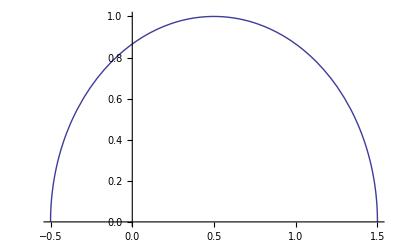

```mathematica
Plot[Sqrt[(t^2)/2-(x-t/2)^2+t/2],{x,-t/2,3t/2}]
```

```mathematica
f[x_]:=Sqrt[(t^2)/2-(x-t/2)^2 +t/2]
```

```mathematica
f[0]
```

6 √2

```mathematica
{Slider[Dynamic[t],{1,20,5}],Dynamic[t]}
Dynamic[Solve[f[x]==0,x]]
```

{,}

```mathematica
t=50
```

50